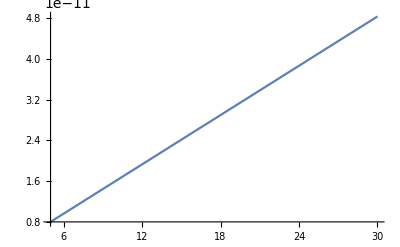

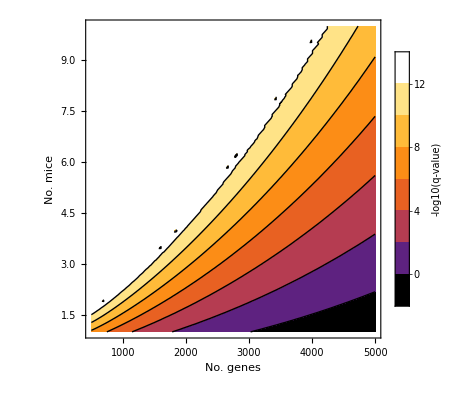

/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV1_27Sep2022.png

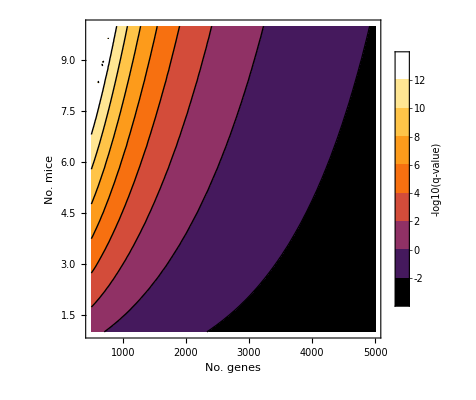

/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV1_27Sep2022.png

```mathematica
z[cles_,n1_,n2_]:=(cles*n1*n2-n1*n2/2)/Sqrt[n1*n2*(n1+n2+1)/12]
p[cles_,n1_,n2_]:=2*Min[{PDF[NormalDistribution[0,1]][z[cles,n1,n2]],
1-PDF[NormalDistribution[0,1]][z[cles,n1,n2]]}]
heff[h_,hexperimental_,hcontrol_, ngenes_,ncell_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h
heffpostengraftment[h_,hexperimental_,hcontrol_, ngenes_,ncell_, engraftmentcorr_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h*engraftmentcorr
p[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,outputengraftmentcorr_]:= p[cles, heff[hexperimental,hexperimental,hcontrol,ngenes, ncell], heffpostengraftment[hcontrol, hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr]]
bonferroni[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,inputengraftmentcorr_,inputengraftmentcorr_]:= p[cles,ngenes,hexperimental,hcontrol,ncell,inputengraftmentcorr, inputengraftmentcorr]*ngenes
fisherscombined[p_,nmice_]:=-2*nmice*Log[p]
fisherscombinedp[p_,nmice_]:=(1-CDF[ChiSquareDistribution[2*nmice]][fisherscombined[p,nmice]])
pcombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_,outputengraftmentcorr_]:=fisherscombinedp[p[cles,ngenes,hexperimental,hcontrol,ncell, outputengraftmentcorr],nmice]
bonferronicombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_, outputengraftmentcorr_]:=pcombined[cles,ngenes,hexperimental,hcontrol,ncell,nmice, outputengraftmentcorr]*ngenes
Plot[bonferronicombined[0.75,ngenes, 96*3,96*10,300000,1,.1],{ngenes, 5,30}]
plot=ContourPlot[-Log[bonferronicombined[3/4,ngenes,96*3,96*10,300000,nmice,1/10]]/Log[10],{ngenes,500,5000},{nmice,1,10},ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"-log10(q-value)"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. genes","No. mice"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20]]

Export["/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV1_27Sep2022.png",plot, ImageResolution->300]
```

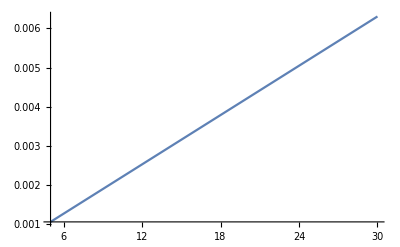

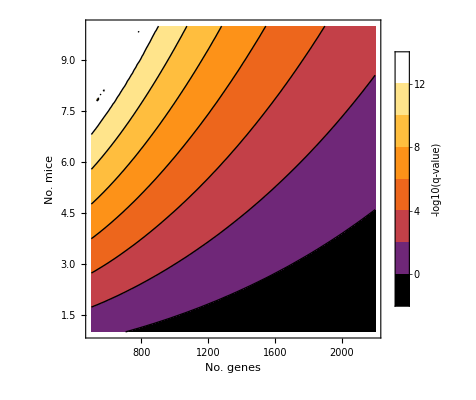

/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV2_27Sep2022.png

```mathematica
z[cles_,n1_,n2_]:=(cles*n1*n2-n1*n2/2)/Sqrt[n1*n2*(n1+n2+1)/12]
p[cles_,n1_,n2_]:=2*Min[{PDF[NormalDistribution[0,1]][z[cles,n1,n2]],
1-PDF[NormalDistribution[0,1]][z[cles,n1,n2]]}]
heff[h_,hexperimental_,hcontrol_, ngenes_,ncell_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h
heffpostengraftment[h_,hexperimental_,hcontrol_, ngenes_,ncell_, engraftmentcorr_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h*engraftmentcorr
p[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,outputengraftmentcorr_]:= p[cles, heffpostengraftment[hexperimental,hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr], heffpostengraftment[hcontrol, hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr]]
bonferroni[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,inputengraftmentcorr_,inputengraftmentcorr_]:= p[cles,ngenes,hexperimental,hcontrol,ncell,inputengraftmentcorr, inputengraftmentcorr]*ngenes
fisherscombined[p_,nmice_]:=-2*nmice*Log[p]
fisherscombinedp[p_,nmice_]:=(1-CDF[ChiSquareDistribution[2*nmice]][fisherscombined[p,nmice]])
pcombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_,outputengraftmentcorr_]:=fisherscombinedp[p[cles,ngenes,hexperimental,hcontrol,ncell, outputengraftmentcorr],nmice]
bonferronicombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_, outputengraftmentcorr_]:=pcombined[cles,ngenes,hexperimental,hcontrol,ncell,nmice, outputengraftmentcorr]*ngenes
Plot[bonferronicombined[0.75,ngenes, 96*3,96*10,300000,1,.1],{ngenes, 5,30}]
plot=ContourPlot[-Log[bonferronicombined[3/4,ngenes,96*3,96*10,300000,nmice,1/10]]/Log[10],{ngenes,500,2200},{nmice,1,10},ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"-log10(q-value)"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. genes","No. mice"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20]]

Export["/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV2_27Sep2022.png",plot,ImageResolution->300]
```

-Graphics-

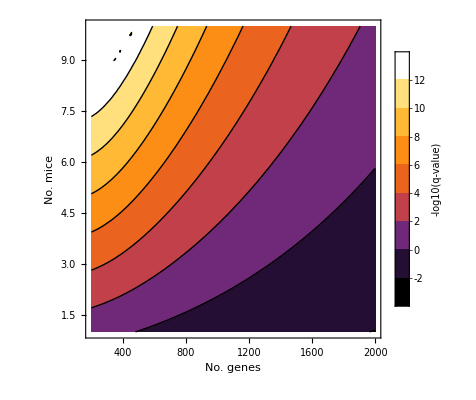

/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV1_TwoPercentEngraftment_27Sep2022.png

```mathematica
z[cles_,n1_,n2_]:=(cles*n1*n2-n1*n2/2)/Sqrt[n1*n2*(n1+n2+1)/12]
p[cles_,n1_,n2_]:=2*Min[{PDF[NormalDistribution[0,1]][z[cles,n1,n2]],
1-PDF[NormalDistribution[0,1]][z[cles,n1,n2]]}]
heff[h_,hexperimental_,hcontrol_, ngenes_,ncell_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h
heffpostengraftment[h_,hexperimental_,hcontrol_, ngenes_,ncell_, engraftmentcorr_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h*engraftmentcorr
p[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,outputengraftmentcorr_]:= p[cles, heff[hexperimental,hexperimental,hcontrol,ngenes, ncell], heffpostengraftment[hcontrol, hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr]]
bonferroni[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,inputengraftmentcorr_,inputengraftmentcorr_]:= p[cles,ngenes,hexperimental,hcontrol,ncell,inputengraftmentcorr, inputengraftmentcorr]*ngenes
fisherscombined[p_,nmice_]:=-2*nmice*Log[p]
fisherscombinedp[p_,nmice_]:=(1-CDF[ChiSquareDistribution[2*nmice]][fisherscombined[p,nmice]])
pcombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_,outputengraftmentcorr_]:=fisherscombinedp[p[cles,ngenes,hexperimental,hcontrol,ncell, outputengraftmentcorr],nmice]
bonferronicombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_, outputengraftmentcorr_]:=pcombined[cles,ngenes,hexperimental,hcontrol,ncell,nmice, outputengraftmentcorr]*ngenes
Plot[bonferronicombined[0.75,ngenes, 96*3,96*10,300000,1,.1],{ngenes, 5,30}]
plot=ContourPlot[-Log[bonferronicombined[3/4,ngenes,96*3,96*10,300000,nmice,2/100]]/Log[10],{ngenes,200,2000},{nmice,1,10},ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"-log10(q-value)"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. genes","No. mice"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20]]

Export["/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV1_TwoPercentEngraftment_27Sep2022.png",plot, ImageResolution->300]
```

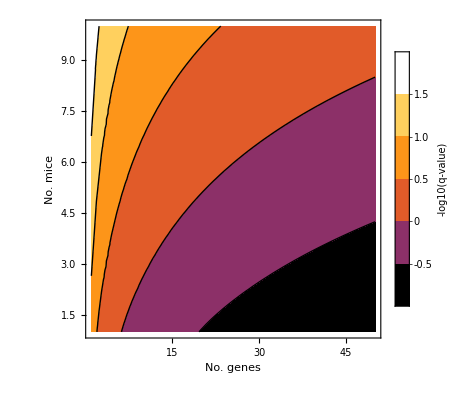

/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV2_TwoPercentEngraftment_27Sep2022.png

```mathematica
z[cles_,n1_,n2_]:=(cles*n1*n2-n1*n2/2)/Sqrt[n1*n2*(n1+n2+1)/12]
p[cles_,n1_,n2_]:=2*Min[{PDF[NormalDistribution[0,1]][z[cles,n1,n2]],
1-PDF[NormalDistribution[0,1]][z[cles,n1,n2]]}]
heff[h_,hexperimental_,hcontrol_, ngenes_,ncell_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h
heffpostengraftment[h_,hexperimental_,hcontrol_, ngenes_,ncell_, engraftmentcorr_]:=(1-CDF[PoissonDistribution[ncell/(ngenes*hexperimental+hcontrol)]][0])*h*engraftmentcorr
p[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,outputengraftmentcorr_]:= p[cles, heffpostengraftment[hexperimental,hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr], heffpostengraftment[hcontrol, hexperimental,hcontrol,ngenes, ncell, outputengraftmentcorr]]
bonferroni[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,inputengraftmentcorr_,inputengraftmentcorr_]:= p[cles,ngenes,hexperimental,hcontrol,ncell,inputengraftmentcorr, inputengraftmentcorr]*ngenes
fisherscombined[p_,nmice_]:=-2*nmice*Log[p]
fisherscombinedp[p_,nmice_]:=(1-CDF[ChiSquareDistribution[2*nmice]][fisherscombined[p,nmice]])
pcombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_,outputengraftmentcorr_]:=fisherscombinedp[p[cles,ngenes,hexperimental,hcontrol,ncell, outputengraftmentcorr],nmice]
bonferronicombined[cles_,ngenes_,hexperimental_,hcontrol_,ncell_,nmice_, outputengraftmentcorr_]:=pcombined[cles,ngenes,hexperimental,hcontrol,ncell,nmice, outputengraftmentcorr]*ngenes
Plot[bonferronicombined[0.75,ngenes, 96*3,96*10,300000,1,.1],{ngenes, 5,30}]
plot=ContourPlot[-Log[bonferronicombined[3/4,ngenes,96*3,96*10,300000,nmice,2/100]]/Log[10],{ngenes,1,50},{nmice,1,10},ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"-log10(q-value)"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. genes","No. mice"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20]]

Export["/home/smarkson/Dropbox (HMS)/CHIME/smarkson_notebooks/figures/PowerCalcV2_TwoPercentEngraftment_27Sep2022.png",plot,ImageResolution->300]
```